# Figure 2 and 4

## Pailin

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
DAT=ReadList["PL-data.txt"];
```

```mathematica
sumall=Import["PLsummary.csv","CSV"];
```

```mathematica
Pid={"P002","P003","P006","P008","P009","P011","P013","P014","P018","P020","P021","P022","P023","P025","P030","P031","P033","P035","P037","P039"};
PidIndx =Thread[Pid->Range[Length@Pid]]
```

{P002→1,P003→2,P006→3,P008→4,P009→5,P011→6,P013→7,P014→8,P018→9,P020→10,P021→11,P022→12,P023→13,P025→14,P030→15,P031→16,P033→17,P035→18,P037→19,P039→20}

```mathematica
DATLength={15,19,15,21,18,12,10,10,15,12,19,15,16,22,11,20,19,11,14,12};
```

```mathematica
times={0,2,4,6,8,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120,126,132,138,144,150,156,162};
```

```mathematica
DetecLim={7.75557,8.20542,8.25334,8.15253,7.41896,7.76042,8.40278,8.15351,7.88173,7.88536,7.84757,7.73046,8.21272,7.81478,7.79295,7.7356,7.43965,8.33122,7.56961,7.78845};
```

```mathematica
ExtractDAT[indx_]:=Thread[{times[[1;;DATLength[[indx]]]],DAT[[indx,1;;DATLength[[indx]]]]}]
```

```mathematica
ExtractPar[indx_]:=Module[{simdat,tls},simdat=(Select[sumall,StringTake[First@#,7+(IntegerDigits[indx]//Length)]=="y_pred["<>ToString@indx&]//Quiet)[[1;;DATLength[[indx]],{5,6,7}]]ᵀ;
tls=times[[1;;DATLength[[indx]]]];
{tls,#}ᵀ&/@simdat
];
```

```mathematica
ExtractPar2[indx_]:=Module[{simdat,tls},simdat=(Select[sumall,StringTake[First@#,12+(IntegerDigits[indx]//Length)]=="ySplit_pred["<>ToString@indx&]//Quiet)[[1;;DATLength[[indx]],{5,6,7}]]ᵀ;
tls=times[[1;;DATLength[[indx]]]];
{tls,#}ᵀ&/@simdat
];
```

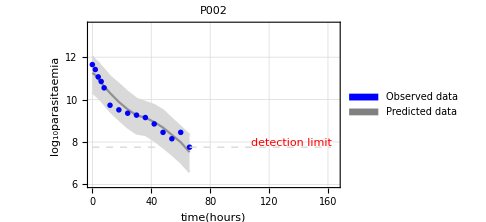

```mathematica
ListPlot[ExtractPar[1]~Join~{ExtractDAT[1]},Joined->{True,True,True,False},PlotRange->{{0,165},{6,13.5}},Frame->True,GridLines->Automatic,Filling->{1->{3}},FillingStyle ->{LightGray},PlotStyle->{LightGray,{Darker@LightGray},LightGray,Blue},FrameLabel->{Style["time(hours)",FontFamily->"Times New Roman",Bold,FontSize->12],Style["log_10parasitaemia",FontFamily->"Times New Roman",Bold,FontSize->12]},PlotLegends->Placed[SwatchLegend[{Blue,Gray},{"Observed data","Predicted data"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.7,0.95},{0.15,1}}],Epilog->{Dashed,LightGray,Line[{{0,DetecLim[[1]]},{162,DetecLim[[1]]}}],Red,Text["detection limit",{135,DetecLim[[1]]+0.2}]},PlotLabel->Pid[[1]],ImageSize->Medium]
```

```mathematica
PlotOutput[indx_Integer]:=ListPlot[ExtractPar[indx]~Join~{ExtractDAT[indx]},Joined->{True,True,True,False},PlotRange->{{0,24*6},{6,13.5}},Frame->True,GridLines->Automatic,Filling->{1->{3}},FillingStyle ->{LightGray},PlotStyle->{LightGray,{Darker@LightGray},LightGray,Blue},FrameLabel->{Style["time(hours)",FontFamily->"Times New Roman",Bold,FontSize->12],Style["log_10parasitaemia",FontFamily->"Times New Roman",Bold,FontSize->12]},PlotLegends->Placed[SwatchLegend[{Blue,Gray},{"Observed data","Predicted data"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.7,0.95},{0.15,1}}],Epilog->{Dashed,LightGray,Line[{{0,DetecLim[[indx]]},{162,DetecLim[[indx]]}}],Red,Text["detection limit",{125,DetecLim[[indx]]}]},PlotLabel->Pid[[indx]],ImageSize->Medium]
```

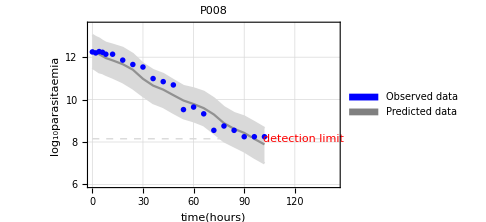
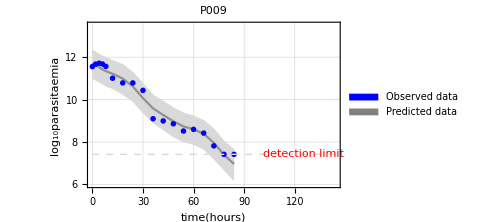
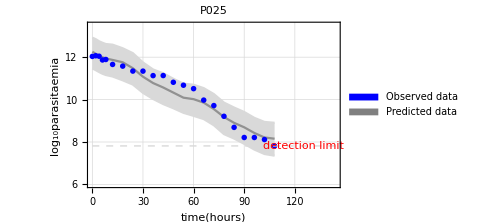
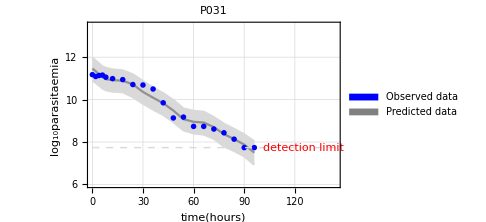

```mathematica
PLGr=PlotOutput[#/.PidIndx]&/@{"P008","P009","P025","P031"}
```

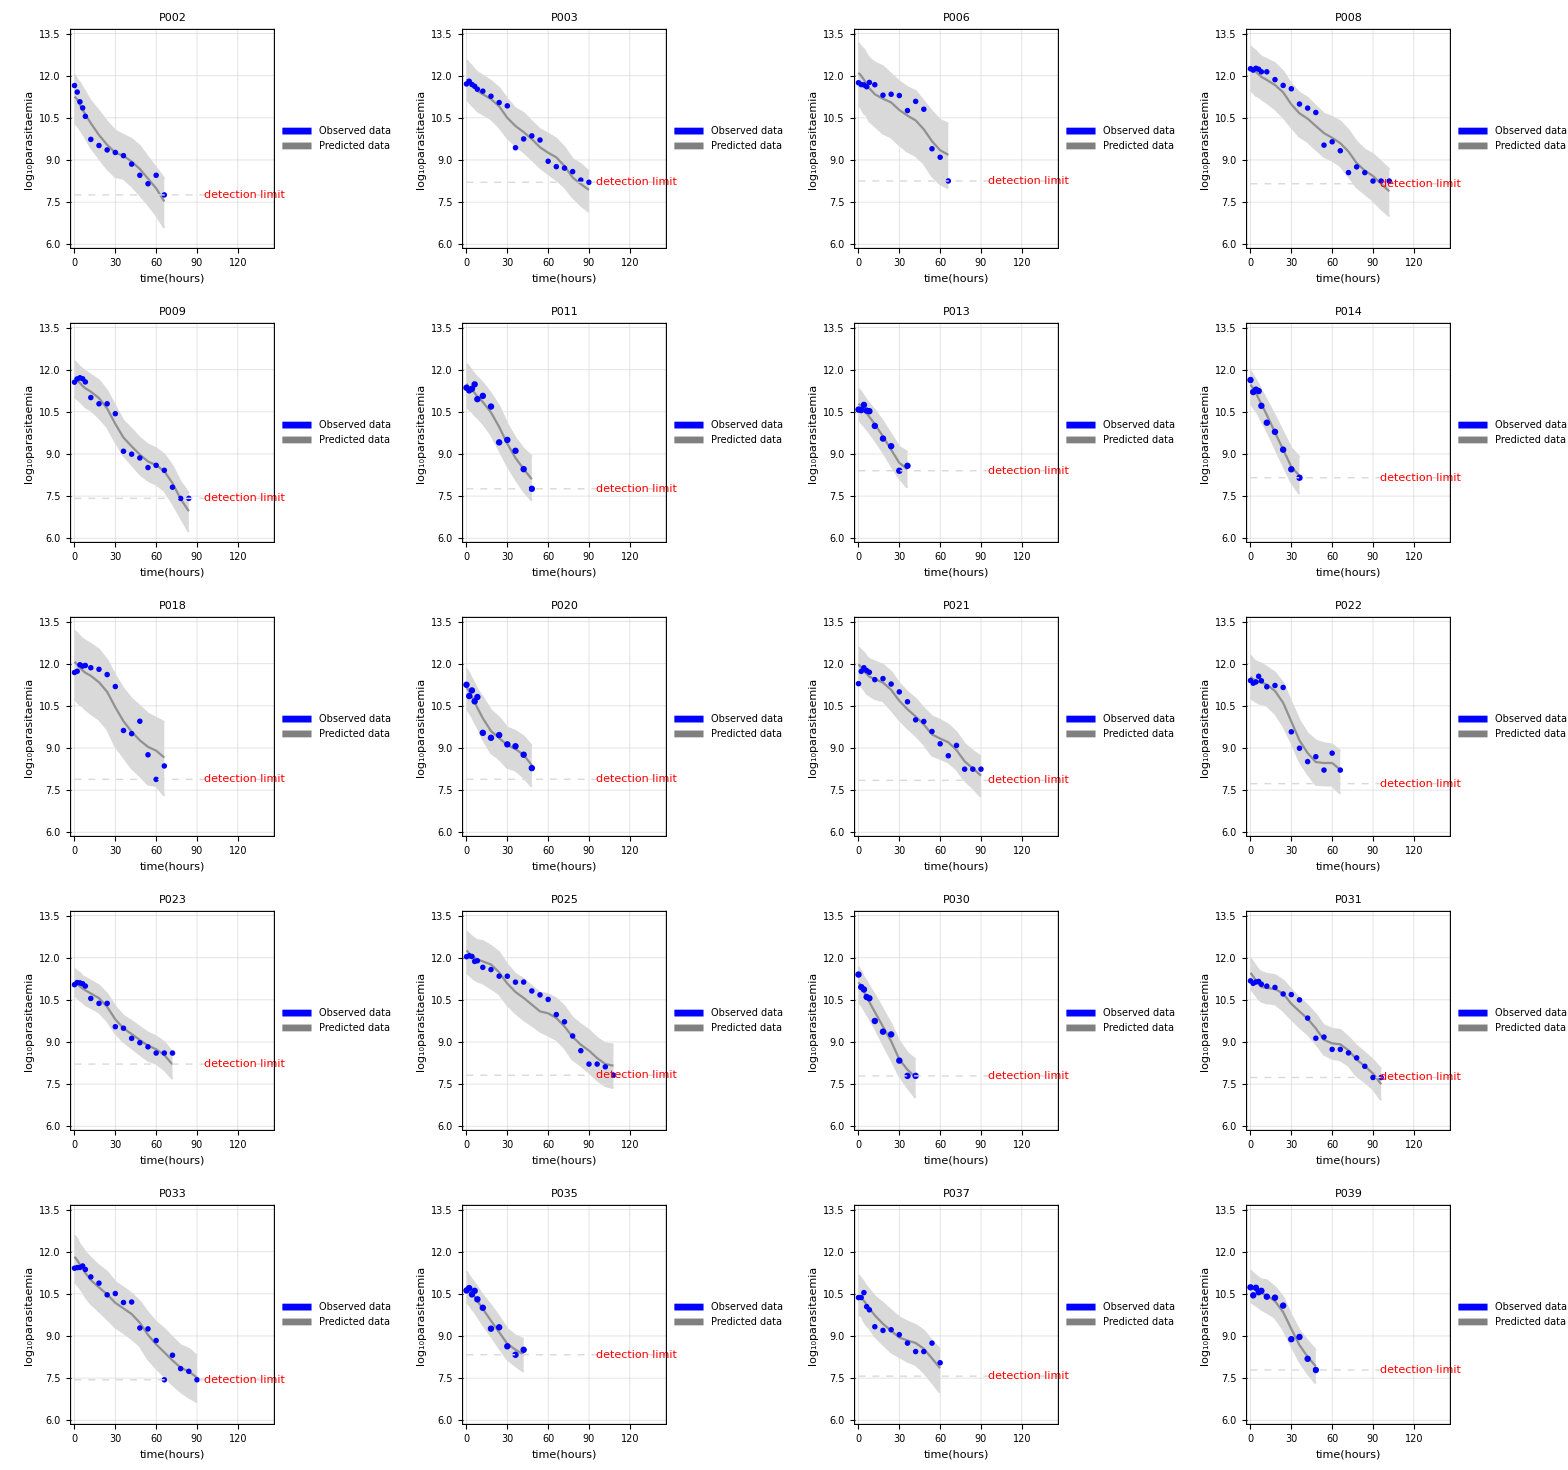

```mathematica
Grid[Partition[PlotOutput/@Range[20],4],Frame->All,ItemSize->All]
```

```mathematica
PlotOutput2[indx_Integer]:=ListPlot[
ExtractPar2[indx]~Join~{ExtractDAT[indx]}~Join~ExtractPar[indx],
Joined->{True,True,True,False,True,True,True},PlotRange->{{0,24*6},{6,13.5}},
Frame->True,GridLines->Automatic,
Filling->{1->{{3},LightGreen},5->{{7},LightPurple}},
PlotStyle->{LightGreen,Green,LightGreen,Black,LightPurple,Lighter@Lighter@Purple,LightPurple},FrameLabel->{Style["time(hours)",FontFamily->"Times New Roman",Bold,FontSize->12],Style["log_10parasitaemia",FontFamily->"Times New Roman",Bold,FontSize->12]},PlotLegends->Placed[SwatchLegend[{Black,Lighter@Lighter@Purple,Green},{"Observed data (every 24 hrs)","Predicted data (every 24 hrs)","Predicted data (every 12 hrs)"},LegendFunction->"Frame",LegendLayout->"Column"],{{0.5,0.95},{0.15,1}}],Epilog->{Dashed,LightGray,Line[{{0,DetecLim[[indx]]},{162,DetecLim[[indx]]}}],Red,Text["detection limit",{125,DetecLim[[indx]]}]},PlotLabel->Pid[[indx]],ImageSize->Medium]
```

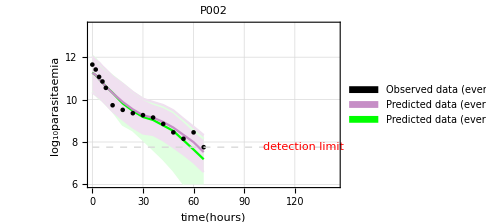

```mathematica
PlotOutput2[1]
```

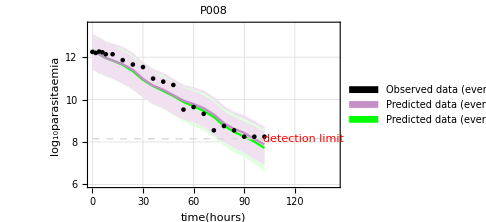
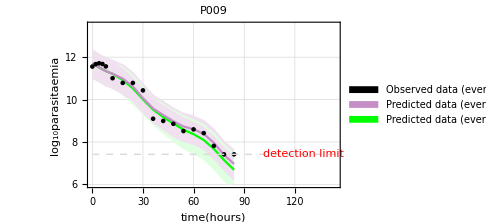
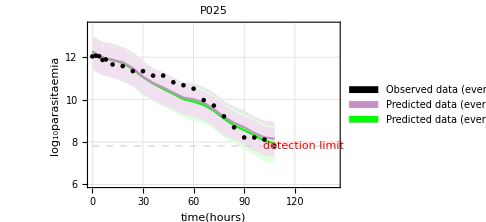
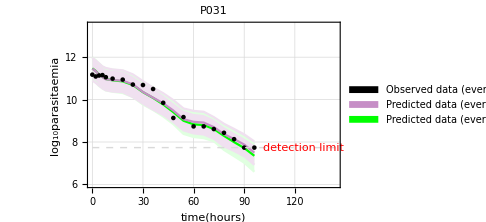

```mathematica
PLGr2=PlotOutput2[#/.PidIndx]&/@{"P008","P009","P025","P031"}
```

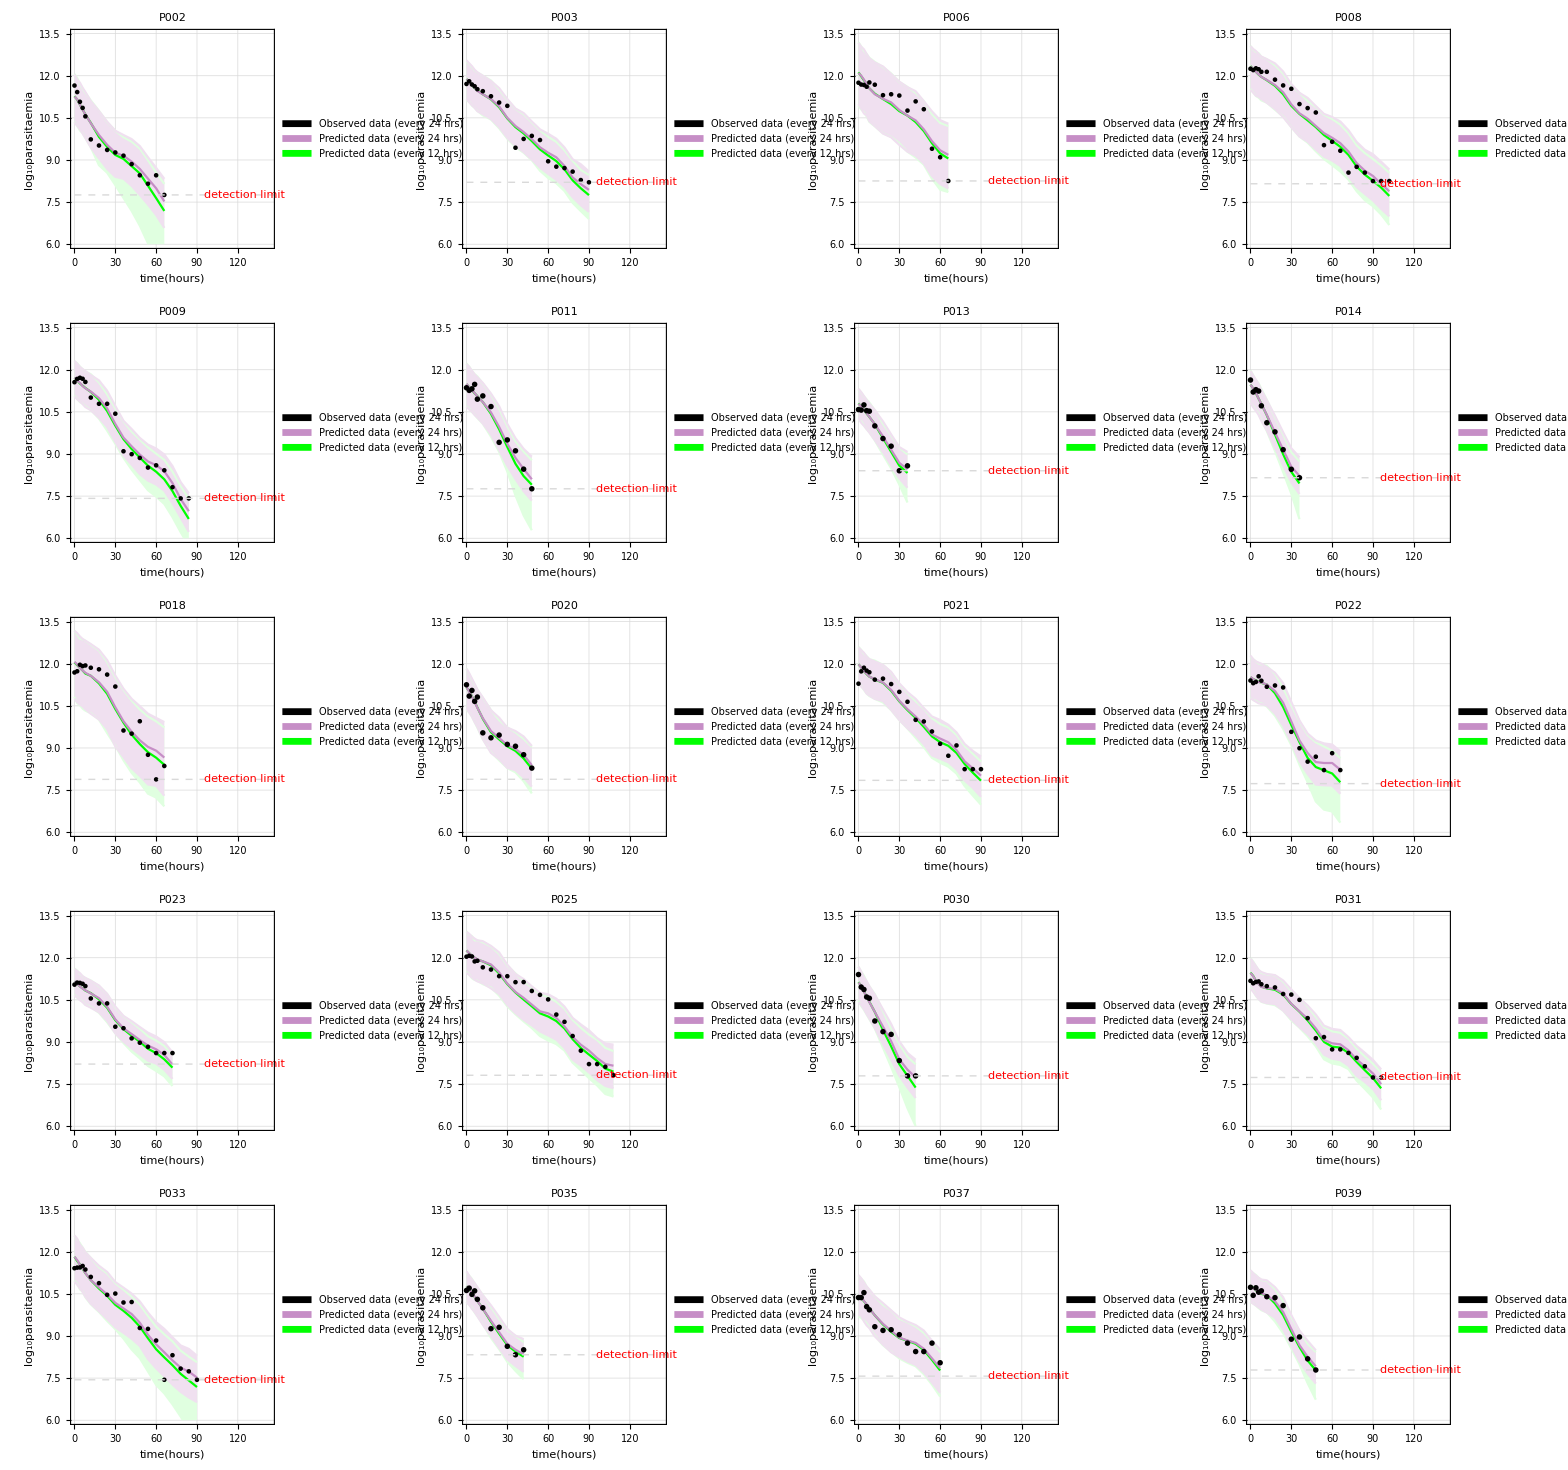

```mathematica
Grid[(PlotOutput2/@Range[20])//Partition[#,4]&,Frame->All]
```